# Polygon Clipping (Suther-Hodgeman Algorithm)

```mathematica
clipper = {{10, 10}, {10, 160}, {260, 160}, {260, 10}};
polygonPoints = {{75, 150}, {25, 200}, {-25, 100}, {0,50}, {75,-25}, {150, 50}, {175,100}, {125,200}};
```

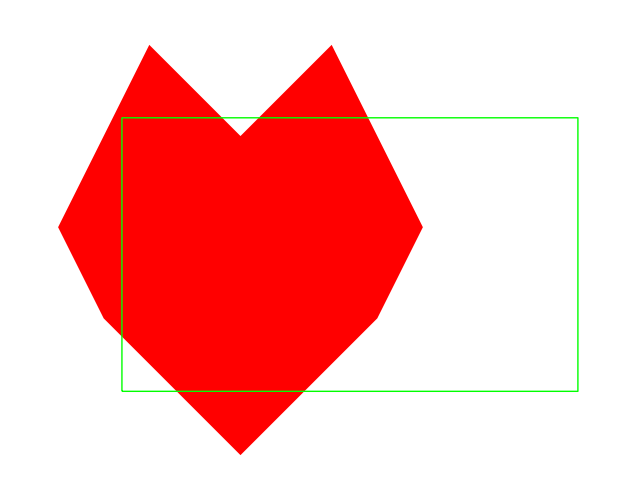

```mathematica
Graphics[{
	Red, Polygon[polygonPoints],
	Green, Line[Append[clipper, First[clipper]]]
}]
```

```mathematica
Intersect[p1_, p2_, p3_, p4_] := Module[{numX, numY, den, x, y},
	den = (p1[[1]] - p2[[1]]) * (p3[[2]] - p4[[2]]) - (p1[[2]] - p2[[2]]) * (p3[[1]] - p4[[1]]);
	If[den == 0, Return[{}]];
	numX = (p1[[1]] p2[[2]] - p1[[2]] p2[[1]]) * (p3[[1]] - p4[[1]]) - (p1[[1]] - p2[[1]]) * (p3[[1]] p4[[2]] - p3[[2]] p4[[1]]);
	numY = (p1[[1]] p2[[2]] - p1[[2]] p2[[1]]) * (p3[[2]] - p4[[2]]) - (p1[[2]] - p2[[2]]) * (p3[[1]] p4[[2]] - p3[[2]] p4[[1]]);
	x = numX / den;
	y = numY / den;
	Return[{x, y}];
];
```

```mathematica
ClipEdge[polygonPoints_, clipperS_, clipperE_] := Module[{i, k, iP, kP, iPos, kPos, newPolygonPoints = {}},
	For[i = 1, i <= Length[polygonPoints], i++,
		k = Mod[i, Length[polygonPoints]] + 1;
		iP = polygonPoints[[i]];
		kP = polygonPoints[[k]];
		
		(* Compute positions relative to the clipping edge *)
		iPos = (clipperE[[1]] - clipperS[[1]]) * (iP[[2]] - clipperS[[2]]) - (clipperE[[2]] - clipperS[[2]]) * (iP[[1]] - clipperS[[1]]);
		kPos = (clipperE[[1]] - clipperS[[1]]) * (kP[[2]] - clipperS[[2]]) - (clipperE[[2]] - clipperS[[2]]) * (kP[[1]] - clipperS[[1]]);
	
		(* Case 1: Both points inside *)
		If[iPos < 0 && kPos < 0,
			AppendTo[newPolygonPoints, kP];
		];
	
		(* Case 2: First point outside, second inside *)
		If[iPos >= 0 && kPos < 0,
			AppendTo[newPolygonPoints, Intersect[clipperS, clipperE, iP, kP]];
			AppendTo[newPolygonPoints, kP];
		];
	
		(* Case 3: First point inside, second outside *)
		If[iPos < 0 && kPos >= 0,
			AppendTo[newPolygonPoints, Intersect[clipperS, clipperE, iP, kP]];
		];
	
		(* Case 4: Both points outside -> No points added *)
	];
	Return[newPolygonPoints];
];
```

```mathematica
SuthHodgClip[clipper_, polygonPoints_] := Module[{i, k, newPolygonPoints = polygonPoints},
	For[i = 1, i <= Length[clipper], i++,
		k = Mod[i, Length[clipper]] + 1;
		newPolygonPoints = ClipEdge[newPolygonPoints, clipper[[i]], clipper[[k]]];
	];
	Return[newPolygonPoints];
];
```

```mathematica
SuthHodgClip[clipper, polygonPoints]
```

{{40,10},{110,10},{150,50},{175,100},{145,160},{85,160},{75,150},{65,160},{10,160},{10,40}}

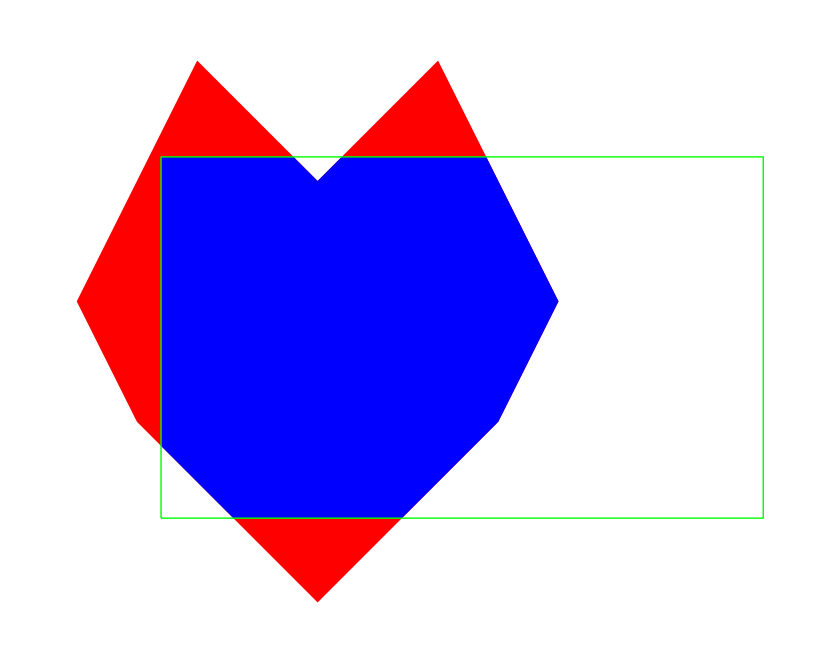

```mathematica
Graphics[{
Red, Polygon[polygonPoints],
   Blue, Polygon[SuthHodgClip[clipper, polygonPoints]], 
   Green, Line[Append[clipper, First[clipper]]]
}]
```